```mathematica
Remove["Global`*"]
```

## Parameters

```mathematica
Nmax=13;
```

```mathematica
k0 = 0.00575;
α300=3.06;
α500 = 6.15;
α1300=30.44;
μ300 = -0.846;
μ500 = 0.356;
μ1300= 1.19;
```

## Markov Equation of the Langmuir kinetics

#### Birth & death rate of occupancy state k

```mathematica
SubPlus[Ω][k_]:= If[k==0, k0*Nmax,k0 *(1-Exp[-α/k])*(Nmax-k)];
SubMinus[Ω][k_]:= If[k==0,0,k0*(1-Exp[-α/k])*Exp[-μ]*k]
```

```mathematica
ClearAll[A,U,Ui,Λ,solDiago,solOri,IC,resCond,solSpecial,m,mean,sd]
```

```mathematica
Do[α=i;
    μ=μ1300;

rowStart={-(SubPlus[Ω][0]),SubMinus[Ω][1], ConstantArray[0,{1,Nmax-1}]}//Flatten;
middle=Table[{ConstantArray[0,{1,k-1}]//Flatten,{SubPlus[Ω][k-1], -(SubPlus[Ω][k]+SubMinus[Ω][k]), SubMinus[Ω][k+1]}, ConstantArray[0,{1,Nmax-(k+1)}]//Flatten}//Flatten,{k,1,Nmax-1}] ;
rowEnd={ConstantArray[0,{1,Nmax-1}],SubPlus[Ω][Nmax-1], -(SubMinus[Ω][Nmax])}//Flatten;

(A[i]=Join[{rowStart}, middle,{rowEnd}])//MatrixForm;

(U[i] = Transpose[Eigenvectors[A[i]]])//MatrixForm;
(Ui[i]=Inverse[U[i]])//MatrixForm;

Λ[i]=Ui[i].A[i].U[i]//Chop//MatrixForm;

solDiago[i][t_]:=Table[c[k]*Exp[Eigenvalues[A[i]][[k]]*t],{k,1,Length[A[i]]}];
(solOri[i]=U[i].solDiago[i][t])//MatrixForm;

(IC[i]=solOri[i]/. t-> 0)//MatrixForm;

resCond[i]=Solve[Table[IC[i][[k]]==If[k==1,1,0],{k,Length[IC[i]]}],Table[c[k],{k,1,Length[IC[i]]}]];
solSpecial[i] = solOri[i]/.resCond[i]//Flatten;

solSpecial[i]/. t-> 100000//MatrixForm;
m[i][t_]:=Sum[solSpecial[i][[k]]*(k-1),{k,1,Length[solSpecial[i]]}];
sd[i][t_]:=Sqrt[Sum[solSpecial[i][[k]]*(k-1)^2,{k,1,Length[solSpecial[i]]}]-m[i][t]^2];

mean[i] = Sum[m[i][t],{t,58000,60000}]/2000;
sd[i] = Sum[sd[i][t],{t,58000,60000}]/2000;

,{i,1,30}
]
```

General::munfl: Exp[-7737.68] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4531.31] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2730.15] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
mean1300 = Table[mean[j],{j,1,30}];
sd1300 = Table[sd[j],{j,1,30}];
```

```mathematica
Needs["ErrorBarPlots`"]
```

General::obspkg: ErrorBarPlots` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
X[J_,μ_]:=1/2(J+μ);
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√(Sinh[X[J,μ]]^2+Exp[-J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+Exp[-J]));
ξ[J_,μ_] := Log[λp[J,μ]/λm[J,μ]]^-1;
Φ[J_,μ_]:= 1/2(1 + Tanh[Nmax/(2ξ[J,μ])] Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) );
Φ2[J_,μ_]:= 1/4(1 + Sinh[X[J,μ]]^2/(Sinh[X[J,μ]]^2+Exp[-J])+Tanh[Nmax/(2ξ[J,μ])]((2Sinh[X[J,μ]])/(√(Sinh[X[J,μ]]^2+Exp[-J]))+1/Nmax (Exp[-J]Cosh[X[J,μ]])/((Sinh[X[J,μ]]^2+Exp[-J])^(3/2))));
σ[J_,μ_]:=√(Φ2[J,μ]-Φ[J,μ]^2);
```

```mathematica
line300=Line[{{1,Φ[0.0000001,μ300]*Nmax},{30,Φ[0.0000001,μ300]*Nmax}}];
line500=Line[{{1,Φ[0.0000001,μ500]*Nmax},{30,Φ[0.0000001,μ500]*Nmax}}];
line1300=Line[{{1,Φ[0.0000001,μ1300]*Nmax},{30,Φ[0.0000001,μ1300]*Nmax}}];
lineStyle={Thick,GrayLevel[0.5],Dashed};
```

```mathematica
Data300 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/BergKMC/Std_study/sdt_vs_Nss_alpha=3.06.dat"];
Data500 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/BergKMC/Std_study/sdt_vs_Nss_alpha=6.15.dat"];
Data1300 = Import["/media/mfranco/Elements/Simulations/Without _depletion/KMC/BergKMC/Std_study/sdt_vs_Nss_alpha=30.44.dat"];
```

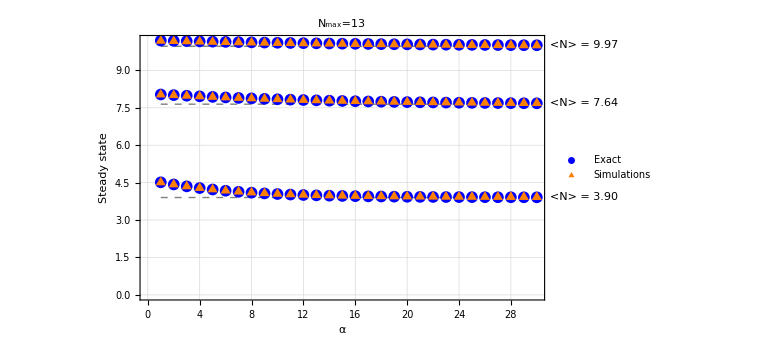

```mathematica
ListPlot[{Labeled[mean300,"<N> = 3.90"],Labeled[mean500, "<N> = 7.64"],Labeled[mean1300,"<N> = 9.97"],Data300[[All,{1,2}]],Data500[[All,{1,2}]],Data1300[[All,{1,2}]]},Epilog->{{Directive[lineStyle],line300},{Directive[lineStyle],line500},{Directive[lineStyle],line1300}},ImageSize->Large,Frame->True,FrameLabel->{"α","Steady state"},PlotMarkers->{Style["•",12,Blue],Style["•",12,Blue],Style["•",12,Blue],Style["▲",12,Orange],Style["▲",12,Orange],Style["▲",12,Orange]},PlotLegends->Placed[LineLegend[{"Exact",None,None,"Simulations",None,None},LegendFunction->Framed],{{0.6,0.2},{0.8,0.5}}],LabelStyle->{12,GrayLevel[0]},PlotLabel->"N_max=13",GridLines->Automatic]
```

```mathematica
SS300 = Φ[0.0000001,μ300]*Nmax;
SS500=Φ[0.0000001,μ500]*Nmax;
SS1300=Φ[0.0000001,μ1300]*Nmax;
SD300 = σ[0.0000001,μ300]*Nmax;
SD500=σ[0.0000001,μ500]*Nmax;
SD1300=σ[0.0000001,μ1300]*Nmax;
```

```mathematica
RD300= (mean300-SS300)/(mean300 + SS300);
RD500 = (mean500-SS500)/(mean500 + SS500);
RD1300 = (mean1300-SS1300)/(mean1300 + SS1300);
```

```mathematica
SDRD300 = 2/(mean300 + SS300)^2(SS300*sd300 - mean300*SD300);
SDRD500 = 2/(mean500 + SS500)^2(SS500*sd500 - mean500*SD500);
SDRD1300 = 2/(mean1300 + SS1300)^2(SS1300*sd1300 - mean1300*SD1300);
```

```mathematica
RD300Dat = Partition[Riffle[RD300,SDRD300],2];
RD500Dat = Partition[Riffle[RD500,SDRD500],2];
RD1300Dat = Partition[Riffle[RD1300,SDRD1300],2];
```

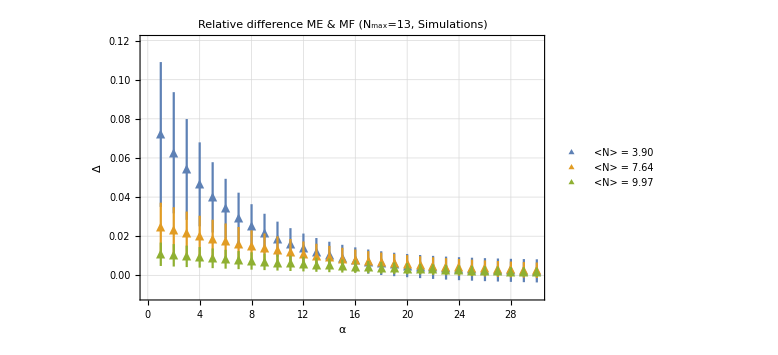

```mathematica
ErrorListPlot[{SimRD300Dat,SimRD500Dat,SimRD1300Dat},ImageSize->Large, Frame->True,GridLines->Automatic,PlotRange->{-0.01,0.12},PlotLegends->Placed[LineLegend[{"<N> = 3.90","<N> = 7.64","<N> = 9.97"},LegendFunction->Framed],{{0.8,0.6},{0.8,0.5}}],LabelStyle->{12,GrayLevel[0]},PlotLabel->"Relative difference ME & MF (N_max=13, Simulations)" , FrameLabel->{"α","Δ"},PlotMarkers->{"▲",12}]
```

```mathematica
SimRD300= (Data300[[All,2]]-SS300)/(Data300[[All,2]] + SS300);
SimRD500 = (Data500[[All,2]]-SS500)/(Data500[[All,2]] + SS500);
SimRD1300 = (Data1300[[All,2]]-SS1300)/(Data1300[[All,2]] + SS1300);
```

```mathematica
SimSDRD300 = 2/(Data300[[All,2]] + SS300)^2(SS300*Data300[[All,3]] - Data300[[All,2]]*SD300);
SimSDRD500 = 2/(Data500[[All,2]] + SS500)^2(SS500*Data500[[All,3]] - Data500[[All,2]]*SD500);
SimSDRD1300 = 2/(Data1300[[All,2]] + SS1300)^2(SS1300*Data1300[[All,3]] - Data1300[[All,2]]*SD1300);
SimRD300Dat = Partition[Riffle[SimRD300,SimSDRD300],2];
SimRD500Dat = Partition[Riffle[SimRD500,SimSDRD500],2];
SimRD1300Dat = Partition[Riffle[SimRD1300,SimSDRD1300],2];
```

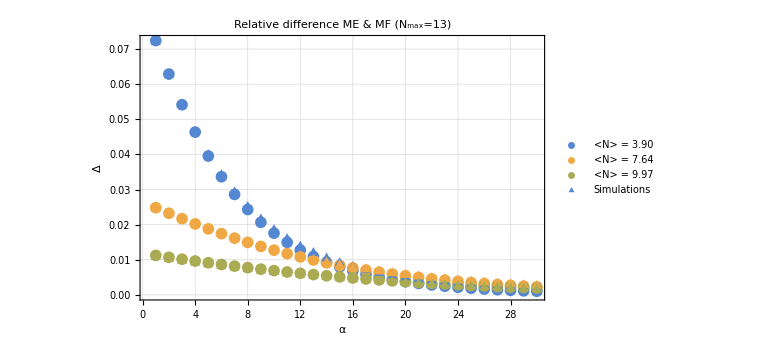

```mathematica
ListPlot[{RD300,RD500,RD1300,SimRD300,SimRD500,SimRD1300},ImageSize->Large, Frame->True,GridLines->Automatic,PlotRange->All,PlotLegends->Placed[LineLegend[{"<N> = 3.90","<N> = 7.64","<N> = 9.97","Simulations"},LegendFunction->Framed],{{0.8,0.6},{0.8,0.5}}],LabelStyle->{12,GrayLevel[0]},PlotLabel->"Relative difference ME & MF (N_max=13)" , FrameLabel->{"α","Δ"},PlotMarkers->{Style["•",12,RGBColor[0.33,0.53,0.82]],Style["•",12,RGBColor[0.94,0.66,0.27]],Style["•",12,RGBColor[0.67,0.67,0.33]],Style["▲",12,RGBColor[0.33,0.53,0.82]],Style["▲",12,RGBColor[0.94,0.66,0.27]],Style["▲",12,RGBColor[0.67,0.67,0.33]]}]
```

```mathematica
Needs["ErrorBarLogPlots`"]
```

Get::noopen: Cannot open ErrorBarLogPlots`.

Needs::nocont: Context ErrorBarLogPlots` was not created when Needs was evaluated.

$Failed

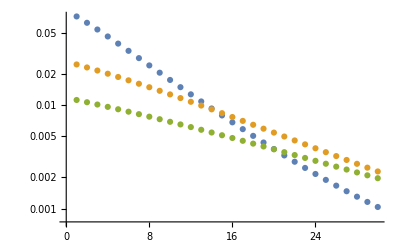

```mathematica
ListLogPlot[{RD300,RD500,RD1300}]
```

```mathematica
l300 = LinearModelFit[Log[RD300],x,x];
Normal[l300]
```

-2.52782-0.149608 x

```mathematica
l500 = LinearModelFit[Log[RD500],x,x];
Normal[l500]
```

-3.55116-0.0835513 x

```mathematica
l1300 = LinearModelFit[Log[RD1300],x,x];
Normal[l1300]
```

-4.38295-0.0607231 x

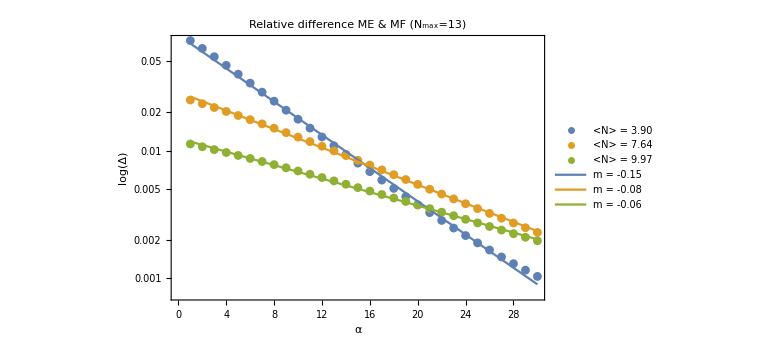

```mathematica
Show[ListLogPlot[{RD300,RD500,RD1300},ImageSize->Large, Frame->True,GridLines->Automatic,PlotLegends->Placed[LineLegend[{"<N> = 3.90","<N> = 7.64","<N> = 9.97"},LegendFunction->Framed],{{0.8,0.7},{0.8,0.5}}],LabelStyle->{12,GrayLevel[0]},PlotLabel->"Relative difference ME & MF (N_max=13)" , FrameLabel->{"α","log(Δ)"}],Plot[{l300[x],l500[x],l1300[x]},{x,1,30},PlotLegends->Placed[LineLegend[{"m = -0.15","m = -0.08","m = -0.06"},LegendFunction->Framed, LegendLabel->"mα + c"],{{0.3,0.3},{0.8,0.7}}]]]
```

```mathematica
Data300[[All,{1,2}]],Data500[[All,{1,2}]],Data1300[[All,{1,2}]]
```

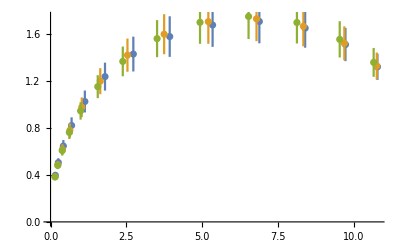

```mathematica
ErrorListPlot[{Data300[[All,{2,3,4}]],Data500[[All,{2,3,4}]],Data1300[[All,{2,3,4}]]}]
```

```mathematica
Data0 = Import["/media/mfranco/Elements/Simulations/Without _depletion/Glauber/Std_vs_Nss/sdt_vs_Nss_J=0_Res.dat"];
Data5=Import["/media/mfranco/Elements/Simulations/Without _depletion/Glauber/SS_Res.dat"];
Data6=Import["/media/mfranco/Elements/Simulations/Without _depletion/Glauber/SS_Stall.dat"];
```

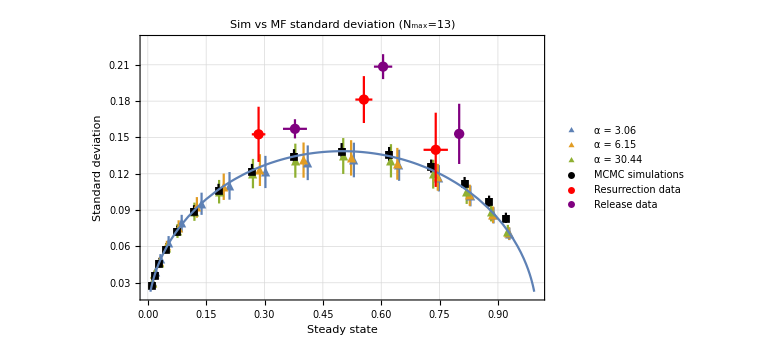

```mathematica
Show[ErrorListPlot[{Data300[[All,{2,3,4}]]/Nmax,Data500[[All,{2,3,4}]]/Nmax,Data1300[[All,{2,3,4}]]/Nmax,Data0[[All,{2,3,4}]]},Frame->True,GridLines->Automatic,ImageSize->Large,PlotRange->{{0,1},{0.02,0.23}},PlotLegends->Placed[LineLegend[{"α = 3.06","α = 6.15","α = 30.44", "MCMC simulations"},LegendFunction->Framed],{{0.6,0.2},{0.8,0.5}}],PlotMarkers->{{"▲",12},{"▲",12},{"▲",12},Style["◼",12,Black]},PlotStyle->{Automatic,Automatic,Automatic,Black},FrameLabel->{"Steady state","Standard deviation"},LabelStyle-> {GrayLevel[0],12}, PlotLabel-> "Sim vs MF standard deviation (N_max=13)"],ParametricPlot[{Φ [0.00000001,μ],σ[0.00000001,μ]}, {μ,-5,5},ImageSize->Large],ErrorListPlot[{{{#1,#2},ErrorBarPlots`ErrorBar@@{#4,#3}}&@@@Data5,{{#1,#2},ErrorBarPlots`ErrorBar@@{#4,#3}}&@@@Data6},PlotStyle->{Red,Purple},PlotLegends->Placed[LineLegend[{"Resurrection data","Release data"},LegendFunction->Framed],{{0.3,0.9},{0.8,0.7}}]]]
```

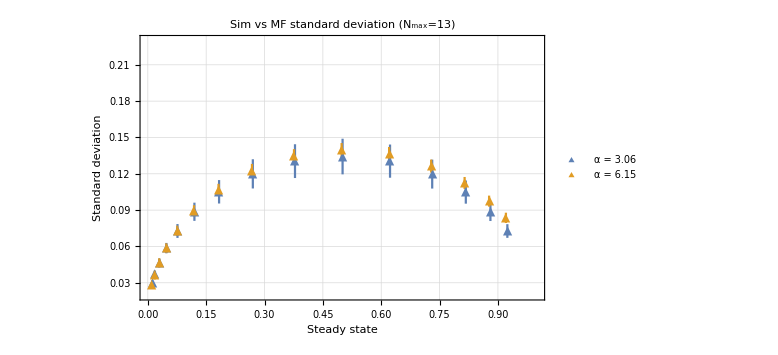

```mathematica
ErrorListPlot[{Data1300[[All,{2,3,4}]]/Nmax,Data0[[All,{2,3,4}]]},Frame->True,GridLines->Automatic,ImageSize->Large,PlotRange->{{0,1},{0.02,0.23}},PlotLegends->Placed[LineLegend[{"α = 3.06","α = 6.15","α = 30.44", "MCMC simulations"},LegendFunction->Framed],{{0.6,0.2},{0.8,0.5}}],PlotMarkers->{{"▲",12},{"▲",12},{"▲",12},Style["◼",12,Black]},PlotStyle->{Automatic,Automatic,Automatic,Black},FrameLabel->{"Steady state","Standard deviation"},LabelStyle-> {GrayLevel[0],12}, PlotLabel-> "Sim vs MF standard deviation (N_max=13)"]
```

## Old

```mathematica
α=1;
μ=μ300;
```

```mathematica
Table[SubPlus[Ω][k],{k,0,Nmax}]
Table[SubMinus[Ω][k],{k,0,Nmax}]
```

{0.07475,0.0436163,0.0248869,0.0162994,0.0114471,0.00833839,0.00617911,0.00459271,0.00337821,0.0024187,0.00164155,0.000999342,0.000459745,0.}

{0,0.00846995,0.0105444,0.0113948,0.0118556,0.0121444,0.0123422,0.0124862,0.0125956,0.0126817,0.0127511,0.0128083,0.0128562,0.0128969}

#### Stochastic matrix

```mathematica
rowStart={-(SubPlus[Ω][0]),SubMinus[Ω][1], ConstantArray[0,{1,Nmax-1}]}//Flatten;
middle=Table[{ConstantArray[0,{1,k-1}]//Flatten,{SubPlus[Ω][k-1], -(SubPlus[Ω][k]+SubMinus[Ω][k]), SubMinus[Ω][k+1]}, ConstantArray[0,{1,Nmax-(k+1)}]//Flatten}//Flatten,{k,1,Nmax-1}] ;
rowEnd={ConstantArray[0,{1,Nmax-1}],SubPlus[Ω][Nmax-1], -(SubMinus[Ω][Nmax])}//Flatten;
```

```mathematica
(A=Join[{rowStart}, middle,{rowEnd}])//MatrixForm
```

(-0.07475 | 0.00846995 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.07475 | -0.0520863 | 0.0105444 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0436163 | -0.0354313 | 0.0113948 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0248869 | -0.0276943 | 0.0118556 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0162994 | -0.0233027 | 0.0121444 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0114471 | -0.0204828 | 0.0123422 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00833839 | -0.0185213 | 0.0124862 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.00617911 | -0.0170789 | 0.0125956 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00459271 | -0.0159739 | 0.0126817 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00337821 | -0.0151004 | 0.0127511 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0024187 | -0.0143926 | 0.0128083 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00164155 | -0.0138076 | 0.0128562 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000999342 | -0.0133159 | 0.0128969
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.000459745 | -0.0128969)

```mathematica
DiagonalizableMatrixQ[A]
```

True

```mathematica
Total[A]//Chop
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(U = Transpose[Eigenvectors[A]])//MatrixForm;
(Ui=Inverse[U])//MatrixForm;
```

```mathematica
Λ=Ui.A.U//Chop//MatrixForm
```

(-0.0938192 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.057901 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.0416598 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.0326566 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.026803 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0225335 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.0191482 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0162839 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.013724 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0113177 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00893674 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00643927 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00361176 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

#### Solution of the decoupled system of linear ODEs

```mathematica
solDiago[t_]:=Table[c[k]*Exp[Eigenvalues[A][[k]]*t],{k,1,Length[A]}]
```

```mathematica
solDiago[t]//MatrixForm;
```

#### Solution of the original system of linear ODEs

```mathematica
(solOri=U.solDiago[t])//MatrixForm;
```

#### Initial conditions

```mathematica
(IC=solOri/. t-> 0)//MatrixForm;
```

#### Find special solution equivalent to resurrection

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]]
```

{{c[1]→-1.88469,c[2]→2.93787,c[3]→-2.4389,c[4]→1.41125,c[5]→0.798061,c[6]→-0.533625,c[7]→0.400518,c[8]→-0.324677,c[9]→-0.279839,c[10]→0.254817,c[11]→-0.24527,c[12]→0.251892,c[13]→-0.284235,c[14]→0.416417}}

```mathematica
solSpecial = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecial[[k]],{k,1,Length[solSpecial]}]/.t->100
```

1.

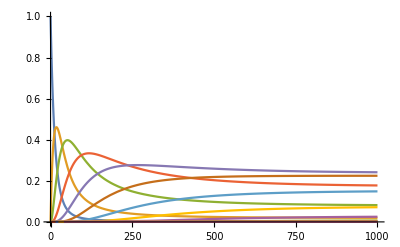

```mathematica
Tmax=1000;
Plot[{solSpecial},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

#### Find special solution equivalent to release after stall

```mathematica
resCond=Solve[Table[IC[[k]]==If[k==Nmax+1,1,0],{k,Length[IC]}],Table[c[k],{k,1,Length[IC]}]]
```

{{c[1]→2.34119×10^-10,c[2]→2.97055×10^-6,c[3]→0.00161506,c[4]→0.093103,c[5]→-1.46642,c[6]→-10.9612,c[7]→-45.1179,c[8]→-110.045,c[9]→165.918,c[10]→156.612,c[11]→91.0026,c[12]→30.8276,c[13]→5.42421,c[14]→0.416417}}

```mathematica
solSpecialStall = solOri/.resCond//Flatten;
```

```mathematica
Sum[solSpecialStall[[k]],{k,1,Length[solSpecial]}]/.t->100
```

1.

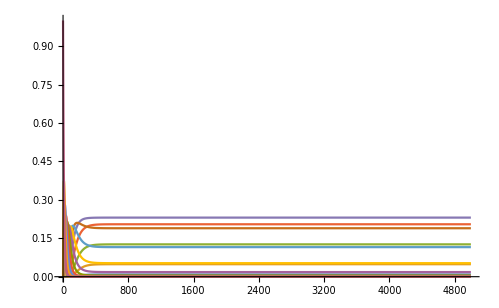

```mathematica
Tmax=5000;
Plot[{solSpecialStall},{t,0,Tmax},PlotRange->{{0,Tmax},{0,1}}]
```

#### Stationary solution

```mathematica
solSpecial/. t-> 100000//MatrixForm
```

General::munfl: Exp[-9381.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-5790.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4165.98] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

(0.00217382
0.0191846
0.0793561
0.173318
0.238283
0.224601
0.15174
0.0750928
0.0273809
0.00729386
0.00138354
0.00017732
0.0000137835
4.91351×10^-7)

#### Mean occupancy for resurrection

```mathematica
m[t_]:=Sum[solSpecial[[k]]*(k-1),{k,1,Length[solSpecial]}]
```

#### Standard Deviation resurrection

```mathematica
sd[t_]:=Sqrt[Sum[solSpecial[[k]]*(k-1)^2,{k,1,Length[solSpecial]}]-m[t]^2]
```

#### Mean occupancy for stall

```mathematica
mStall[t_]:=Sum[solSpecialStall[[k]]*(k-1),{k,1,Length[solSpecialStall]}]
```

#### Standard Deviation stall

```mathematica
sdStall[t_]:=Sqrt[Sum[solSpecialStall[[k]]*(k-1)^2,{k,1,Length[solSpecialStall]}]-mStall[t]^2]
```

#### Plots

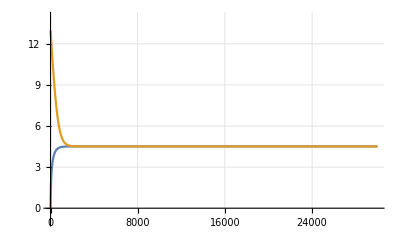

```mathematica
Tmax=30000;
plot=Show[Plot[{m[t],mStall[t]},{t,0.1,Tmax},PlotRange->{{0,Tmax},{-1,Nmax+1}},GridLines->Automatic, TargetUnits->"Minutes"]]
```

## Langmuir

```mathematica
X[J_,μ_]:=1/2(J+μ);
λp[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]+√(Sinh[X[J,μ]]^2+Exp[-J]));
λm[J_,μ_]:= Exp[X[J,μ]](Cosh[X[J,μ]]-√(Sinh[X[J,μ]]^2+Exp[-J]))
```

```mathematica
ξ[J_,μ_] := Log[λp[J,μ]/λm[J,μ]]^-1;
```

```mathematica
Φ[J_,μ_]:= 1/2(1 + Tanh[Nmax/(2ξ[J,μ])] Sinh[X[J,μ]]/(√(Sinh[X[J,μ]]^2+ Exp[-J])) )
```

## Comparison

```mathematica
Φ[0.0000001,μ500]*Nmax
```

7.64493

```mathematica
mean1 = Sum[m[t],{t,3000,5000}]/2000
sd1 = Sum[sd[t],{t,3000,5000}]/2000
```

General::munfl: -9.09277×10^-8 2.41319×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

4.04327

General::munfl: -9.09277×10^-8 2.41319×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

1.68977

```mathematica
alarray =  {1,2,3,4,5,6,7,8,9,10};
```

```mathematica
meanarray300 = {mean01,mean02,mean03,mean04,mean05,mean06,mean07,mean08,mean09,mean1};
sdarray300 = {sd01,sd02,sd03,sd04,sd05,sd06,sd07,sd08,sd09,sd1};
```

## α dependence

```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
Which[alarray=0.1]
```

Which::argctu: Which called with 1 argument.

Which[alarray=0.1]

```mathematica
Data300=List[alarray,meanarray300]
```

{{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1},{4.59409,4.58477,4.57536,4.56601,4.55672,4.54748,4.53831,4.5292,4.52016,4.51118}}

```mathematica
Data300[[1]]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1}

```mathematica
Data300[[2]]
```

{4.59409,4.58477,4.57536,4.56601,4.55672,4.54748,4.53831,4.5292,4.52016,4.51118}

```mathematica
line=Line[{{1,Φ[0.0000001,μ300]*Nmax},{10,Φ[0.0000001,μ300]*Nmax}}]
```

Line[{{0,3.90354},{10,3.90354}}]

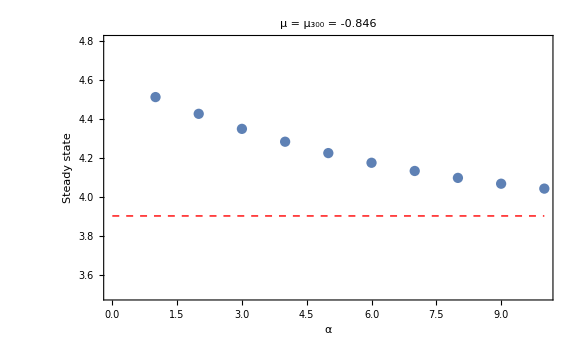

Line[3.90354]

```mathematica
lineStyle={Thick,Red,Dashed};
Show[Plot[0,{x,1,10},Epilog->{Directive[lineStyle],line},PlotRange->{3.5,4.8},ImageSize->Large, Frame->True, PlotLabel->"μ = μ_300 = -0.846",LabelStyle->{12,GrayLevel[0]},FrameLabel->{"α","Steady state"}],ListPlot[{{alarray[[1]],meanarray300[[1]]},{alarray[[2]],meanarray300[[2]]},{alarray[[3]],meanarray300[[3]]},{alarray[[4]],meanarray300[[4]]},{alarray[[5]],meanarray300[[5]]},{alarray[[6]],meanarray300[[6]]},{alarray[[7]],meanarray300[[7]]},{alarray[[8]],meanarray300[[8]]},{alarray[[9]],meanarray300[[9]]},{alarray[[10]],meanarray300[[10]]}}]]
```

## Dwell time: zero occupancy

```mathematica
p=Table[k*(β-α)+α*Nmax,{k,0,Nmax}];
λ=-Log[1-p]
```

{0.0326368,0.0317074,0.0307788,0.0298511,0.0289243,0.0279983,0.0270732,0.0261489,0.0252255,0.0243029,0.0233812,0.0224604,0.0215403,0.0206212}